# Deriving the metric

## I. Differential geometry entities

```mathematica
Coords={t,r,θ,ϕ};
Dim=Length[Coords];
```

Plug in the metric ansatz and calculate its inverse

```mathematica
Met=DiagonalMatrix[{-ⅇ^f[r],ⅇ^g[r],ⅇ^g[r] r^2,ⅇ^g[r] r^2 Sin[θ]^2}];
InvMet=Inverse[Met];
```

From it, the Christoffel symbols and curvatures follow.

```mathematica
Christoff=Table[1/2∑_(μ=1)^Dim (InvMet⟦σ,μ⟧(D[Met⟦μ,β⟧,Coords⟦α⟧]+D[Met⟦μ,α⟧,Coords⟦β⟧]-D[Met⟦α,β⟧,Coords⟦μ⟧])),{σ,1,Dim},{α,1,Dim},{β,1,Dim}];
Curv=Table[(D[Christoff⟦i,j,l⟧, Coords⟦k⟧]+∑_(s=1)^Dim Christoff⟦s,j,l⟧Christoff⟦i,s,k⟧-D[Christoff⟦i,j,k⟧, Coords⟦l⟧]-∑_(s=1)^Dim Christoff⟦s,j,k⟧Christoff⟦i,s,l⟧),{i,1,Dim},{j,1,Dim},{k,1,Dim},{l,1,Dim}];
Ric=Table[∑_(i=1)^Dim Curv⟦i,j,i,l⟧,{j,1,Dim},{l,1,Dim}];
ScalRic=∑_(i=1)^Dim ∑_(j=1)^Dim InvMet⟦i,j⟧Ric⟦i,j⟧;
```

## II. Einstein’s equations

We have the Einstein tensor

```mathematica
EinsTens=Table[Ric⟦μ,ν⟧-1/2 ScalRic Met⟦μ,ν⟧,{μ,1,Dim},{ν,1,Dim}]//Simplify;
EinsTens//MatrixForm
```

(-(ⅇ^(f[r]-g[r]) (8 g'[r]+r g'[r]^2+4 r g''[r]))/(4 r) | 0 | 0 | 0
0 | (2 f'[r] (2+r g'[r])+g'[r] (4+r g'[r]))/(4 r) | 0 | 0
0 | 0 | 1/4 r (2 f'[r]+r f'[r]^2+2 (g'[r]+r (f''[r]+g''[r]))) | 0
0 | 0 | 0 | 1/4 r Sin[θ]^2 (2 f'[r]+r f'[r]^2+2 (g'[r]+r (f''[r]+g''[r]))))

Let the stress-energy tensor be

```mathematica
MixStressTens=DiagonalMatrix[{-ρ,0,Subscript[P, t],Subscript[P, t]}];
StressTens=Table[∑_(α=1)^Dim (Met⟦μ,α⟧MixStressTens⟦α,ν⟧),{μ,1,Dim},{ν,1,Dim}];
InvStressTens=Table[∑_(α=1)^Dim (InvMet⟦ν,α⟧MixStressTens⟦μ,α⟧),{μ,1,Dim},{ν,1,Dim}];
```

```mathematica
StressTens//MatrixForm
```

(ⅇ^f[r] ρ | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | ⅇ^g[r] r^2 P_t | 0
0 | 0 | 0 | ⅇ^g[r] r^2 Sin[θ]^2 P_t)

The f' equation must be

```mathematica
fEqn=f'[r]/.Solve[EinsTens⟦2,2⟧==8π StressTens⟦2,2⟧,f'[r]]⟦1⟧//FullSimplify
```

-(g'[r] (4+r g'[r]))/(4+2 r g'[r])

and the density function must be

```mathematica
rhoEqn=ρ/.Solve[EinsTens⟦1,1⟧==8π StressTens⟦1,1⟧,ρ]⟦1⟧//Simplify
```

-(ⅇ^(-g[r]) (8 g'[r]+r g'[r]^2+4 r g''[r]))/(32 π r)

Take ∇_β T^αβ so that we can state the conservation law. First, we define a function that takes the covariant derivative of (2,0) tensor.

```mathematica
CovDev[α_]:=Table[(∑_(b=1)^Dim D[α⟦a,b⟧, Coords⟦b⟧]+∑_(b=1)^Dim ∑_(u=1)^Dim α⟦u,b⟧Christoff⟦a,u,b⟧+∑_(b=1)^Dim ∑_(u=1)^Dim α⟦a,u⟧Christoff⟦b,u,b⟧),{a,1,Dim}];
```

```mathematica
CovStressTens=CovDev[InvStressTens];
```

```mathematica
CovStressTens//MatrixForm
```

(0
1/2 ⅇ^(-g[r]) ρ f'[r]+(ⅇ^(-2 g[r]) P_t (-2 ⅇ^g[r] r-ⅇ^g[r] r^2 g'[r]))/(2 r^2)+(ⅇ^(-2 g[r]) Csc[θ]^2 P_t (-2 ⅇ^g[r] r Sin[θ]^2-ⅇ^g[r] r^2 Sin[θ]^2 g'[r]))/(2 r^2)
0
0)

From this, we get the pressure equation

```mathematica
pEqn=FullSimplify[Subscript[P, t]/.Solve[CovStressTens⟦2⟧==0,Subscript[P, t]]/.f'[r]->fEqn]⟦1⟧
```

ρ (-1/4+1/(2+r g'[r])^2)

## III. Vanishing density condition

Let’s assume a g(r) of the form

```mathematica
g[r_]:=Log[(1+R/r-ϕ[r](1-R/r)^μ)^(4+ν)]
```

where R is the location of the event horizon. We only want to consider μ=1 and μ>=2 to avoid the divergence of the density function in the horizon. For μ=1,

```mathematica
RhoMu1=rhoEqn/.μ->1/.r->R//Simplify
```

-(2^(-11-ν) (4+ν) (ν+2 ν ϕ[R]+ν ϕ[R]^2-16 R ϕ'[R]))/(π R^2)

We get the condition

```mathematica
Mu1DensCond=Solve[RhoMu1==0,ν]//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ν→-4},{ν→(16 R ϕ'[R])/(1+ϕ[R])^2}}

For μ=2

```mathematica
RhoMu2=rhoEqn/.μ->2/.r->R//Simplify
```

-(2^(-11-ν) (4+ν) (ν-16 ϕ[R]))/(π R^2)

```mathematica
Mu2DensCond=Solve[RhoMu2==0,ν]//Simplify
```

{{ν→-4},{ν→16 ϕ[R]}}

For μ>2

```mathematica
RhoMuG2=rhoEqn/.r->R//Simplify[#,μ>2]&
```

-(2^(-11-ν) ν (4+ν))/(π R^2)

```mathematica
MuG2DensCond=Solve[RhoMuG2==0,ν]//Simplify
```

{{ν→-4},{ν→0}}

## IV. Horizon condition

## Case I: μ=1

Check the value of f' around the horizon in the case where μ=1

```mathematica
fHor1=fEqn/.μ->1/.Mu1DensCond⟦2⟧/.r->R//Simplify
```

((-1+ϕ[R]^2+4 R ϕ'[R]) (1+2 ϕ[R]+ϕ[R]^2+4 R ϕ'[R]))/(R (1+ϕ[R]) (ϕ[R]+ϕ[R]^2+4 R ϕ'[R]))

We want this term to be divergent.  To make this happen, we want

```mathematica
Mu1MetCond=Solve[Denominator[fEqn/.μ->1/.Mu1DensCond⟦2⟧/.r->R//Simplify]==0,ϕ'[R]]
```

{{ϕ'[R]→-(ϕ[R] (1+ϕ[R]))/(4 R)}}

## Case II: μ=2

Evaluate f' at r=R

```mathematica
fHor2=fEqn/.μ->2/.Mu2DensCond⟦2⟧/.r->R//Simplify
```

(-1+16 ϕ[R]^2)/(4 R ϕ[R])

The only way to make this singular is to set

```mathematica
Mu2MetCond=Solve[Denominator[fEqn/.μ->2/.Mu2DensCond⟦2⟧/.r->R]==0,ϕ[R]]
```

{{ϕ[R]→0}}

## Case II: μ>2

Evaluate f' at r=R

```mathematica
fHor3=fEqn/.MuG2DensCond⟦2⟧/.μ->2+τ//Simplify[#,τ>0]&
```

-(4 ((r-R) (1-R/r)^τ (r+R+R τ) ϕ[r]+r (-r+(r-R)^2 (1-R/r)^τ ϕ'[r])) ((r-R) R (1-R/r)^τ (2+τ) ϕ[r]+r (R+(r-R)^2 (1-R/r)^τ ϕ'[r])))/(r (r-R) (-r (r+R)+(r-R)^2 (1-R/r)^τ ϕ[r]) ((1-R/r)^τ (r+R (3+2 τ)) ϕ[r]+r (-1+2 (r-R) (1-R/r)^τ ϕ'[r])))

It is already divergent at the horizon.

## V. Weak field

Take the first case μ=1. Parametrize the Hernquist potential function to determine the horizon condition

```mathematica
Solve[(ϕ'[R]+(ϕ[R] (1+ϕ[R]))/(4 R)/.ϕ->Function[r,-M/(a+k r)])==0,R]
```

{{R→(a-M)/(3 k)}}

Then, we take the weak field limit, assuming a small compactness.

```mathematica
nondimWeakField=Series[Exp[g[r]]/.μ->1/.Mu1DensCond⟦2⟧/.ϕ->Function[r,-M/(a+k r)]/.M->c a/.R->σ a/.r-> r a/.a->1/.σ->(1-c)/(3k)//Simplify,{c,0,1},{r,∞,1}]//Normal//Expand
```

1+4/(3 k r)+(11 c)/(3 k r)

```mathematica
Exp[g[r]]/.μ->1/.Mu1DensCond⟦2⟧/.ϕ->Function[r,-M/(a+k r)]/.M->c a/.R->σ a/.r-> r a/.a->1/.σ->(1-c)/(3k)/.k->5/2//Simplify
```

((4-8 c+4 c^2+40 r+20 c r+75 r^2)/(30 r+75 r^2))^((-4+c)/(-1+c))

We plug the dimensional quantities back in, again.

```mathematica
nondimWeakField/.r->r/a/.c->M/a/.a->3k R+M//Expand
```

1+(5 M)/(k r)+(4 R)/r

To recreate the expected Newtonian metric,  let k=5/2. This implies that for the horizon condition to be satisfied, R must be at 2(a-M)/15.

## VI. Metric

## Case: μ=1

Setting up the differential equation for f given the location of the horizon and k, we must have

```mathematica
fDE1=fEqn/.μ->1/.Mu1DensCond⟦2⟧/.ϕ->Function[r,-M/(a+k r)]/.R->(a-M)/(3k)/.k->5/2//Expand//FullSimplify
```

((4 a-M) (4 a (a-M)^2+20 (a-M)^2 r+25 (a+2 M) r^2) (12 a (a-M)^2 M-20 (a-M) (2 a+M) (3 a+M) r-75 (8 a^2-9 a M-2 M^2) r^2+750 (-a+M) r^3))/((a-M) (2 a-2 M-15 r) r (2 a+5 r) (4 (a-M)^2+20 (2 a+M) r+75 r^2) (2 a (a-M) (2 a+M)+5 a (4 a-7 M) r+25 (a-M) r^2))

The metric function must be

```mathematica
fTent1=Exp[Integrate[fDE1,r]//Expand]//Simplify[#,{Element[{a,M,r},Reals],a>0,M>0,r>0}]&
```

ⅇ^(((8 a^2+23 a M-4 M^2) ArcTan[(4 a^2-7 a M+10 a r-10 M r)/(√(a M (32 a^2-49 a M+8 M^2)))])/((2 a+M) √(a (-49 a+(32 a^2)/M+8 M)))) r^((3 (4 a-M) M)/(2 (a-M) (2 a+M))) (-2 a+2 M+15 r)^2 ((2 a+5 r)/(4 a^2-8 a M+4 M^2+40 a r+20 M r+75 r^2))^((4 a-M)/(2 a-2 M)) (4 a^3-2 a^2 (M-10 r)-25 M r^2+a (-2 M^2-35 M r+25 r^2))^(-(3 M)/(4 a+2 M))

As r approaches infinity, the limit must be

```mathematica
fTentLim=Limit[ⅇ^(((8 a^2+23 a M-4 M^2) (π/2))/((2 a+M) √(a (-49 a+(32 a^2)/M+8 M)))) r^((3 (4 a-M) M)/(2 (a-M) (2 a+M))) (15 r)^2 ((5 r)/(75 r^2))^((4 a-M)/(2 a-2 M)) (-25 M r^2+a (25 r^2))^(-(3 M)/(4 a+2 M)),r->∞]
```

3^(-(3 M)/(2 a-2 M)) 5^(-(3 (4 a-M) M)/(2 (a-M) (2 a+M))) ⅇ^(((8 a^2+23 a M-4 M^2) π)/(2 (2 a+M) √(a (-49 a+(32 a^2)/M+8 M)))) (a-M)^(-(3 M)/(4 a+2 M))

Normalizing, we get the actual metric function

```mathematica
Met1=fTent1/fTentLim//Simplify[#,{Element[{a,M,r},Reals],a>0,M>0,r>0,a>M}]&
```

5^((3 (4 a-M) M)/(2 (a-M) (2 a+M))) 27^(M/(2 a-2 M)) ⅇ^(-((8 a^2+23 a M-4 M^2) (π-2 ArcTan[(4 a^2-7 a M+10 a r-10 M r)/(√(a M (32 a^2-49 a M+8 M^2)))]))/(2 (2 a+M) √(a (-49 a+(32 a^2)/M+8 M)))) r^((3 (4 a-M) M)/(2 (a-M) (2 a+M))) (-2 a+2 M+15 r)^2 ((2 a+5 r)/(4 a^2-8 a M+4 M^2+40 a r+20 M r+75 r^2))^((4 a-M)/(2 a-2 M)) ((4 a^3-2 a^2 (M-10 r)-25 M r^2+a (-2 M^2-35 M r+25 r^2))/(a-M))^(-(3 M)/(4 a+2 M))

We can have the nondimensional version.

```mathematica
FinalMet=Met1/.M->c a/.a->1//Simplify
```

5^((3 (-4+c) c)/(2 (-2+c+c^2))) 27^(c/(2-2 c)) ⅇ^(((-8-23 c+4 c^2) (π-2 ArcTan[(4+10 r-c (7+10 r))/(√(c (32-49 c+8 c^2)))]))/(2 (2+c) √(-49+32/c+8 c))) r^((3 (-4+c) c)/(2 (-2+c+c^2))) (-2+2 c+15 r)^2 ((2+5 r)/(4-8 c+4 c^2+40 r+20 c r+75 r^2))^((-4+c)/(2 (-1+c))) ((2 c^2-(2+5 r)^2+c (2+35 r+25 r^2))/(-1+c))^(-(3 c)/(4+2 c))

What is its weak field limit?

```mathematica
wfgtt=Series[FinalMet,{c,0,1},{r,∞,1}]//Simplify[#,{Element[{c,r},Reals],c>0,r>0,c<1}]&//Normal
```

1-8/(15 r)-(22 c)/(15 r)

```mathematica
wfgtt/.r->r/a/.c->M/a/.a->3k R+M/.k->5/2//Expand
```

1-(2 M)/r-(4 R)/r

Check its behavior

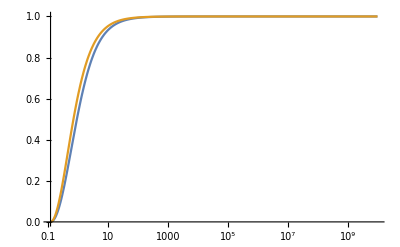

```mathematica
c=0.1;
σ=(2(1-c))/15;
LogLinearPlot[{FinalMet,((1-σ/r)/(1+σ/r))^2},{r,σ,10^10},PlotRange->Full]
Clear[c,σ]
```

Does it reduce to Schwarzschild?

```mathematica
Series[FinalMet,{c,0,0}]//Simplify[#,{Element[{c,r},Reals],c>0,r>0}]&
```

(2-15 r)^2/(2+15 r)^2+O[c]^1

Yes.

Is the density always positive?

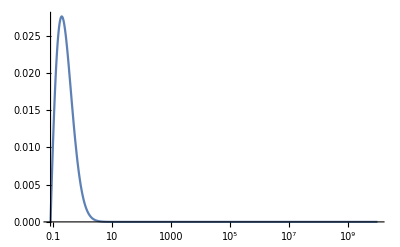

```mathematica
c=0.4;
σ=(2(1-c))/15;
LogLinearPlot[{rhoEqn/.μ->1/.Mu1DensCond⟦2⟧/.R->σ a/.M->c a/.a->1/.ϕ->Function[r,-c/(1+5/2 r)]},{r,σ,10^10},PlotRange->Full]
Clear[c,σ]
```

Check which values of c will make ρ negative

```mathematica
rhoZeros=r/.Solve[Numerator[(rhoEqn/.μ->1/.Mu1DensCond⟦2⟧/.R->σ a/.M->c a/.a->1/.ϕ->Function[r,-c/(1+5/2 r)]/.σ->2/15(1-c)//Simplify)]==0,r]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{-2/15 (-1+c),(40-30 0^(-(1-c)/c)+20 c-√((-40+30 0^(-(1-c)/c)-20 c)^2-4 (-75+75 0^(-(1-c)/c)) (-4+8 c-4 c^2)))/(150 (-1+0^(-(1-c)/c))),(40-30 0^(-(1-c)/c)+20 c+√((-40+30 0^(-(1-c)/c)-20 c)^2-4 (-75+75 0^(-(1-c)/c)) (-4+8 c-4 c^2)))/(150 (-1+0^(-(1-c)/c))),(2 (-49+57 c-12 c^2+4 c^3))/(15 (31-44 c+4 c^2))+(-1120000-5520000 c+17850000 c^2-14860000 c^3+3810000 c^4-120000 c^5-40000 c^6)/(37500 (31-44 c+4 c^2) (1628+12753 c-56358 c^2+80247 c^3-55665 c^4+23670 c^5-7509 c^6+1278 c^7-36 c^8-8 c^9+9 √(15376+256184 c-692223 c^2-9113156 c^3+62543114 c^4-186410334 c^5+332227450 c^6-389138890 c^7+310241520 c^8-169404538 c^9+62415973 c^10-14935602 c^11+2141558 c^12-145664 c^13-1536 c^14+800 c^15-32 c^16))^(1/3))-1/(15 (31-44 c+4 c^2))4 (1628+12753 c-56358 c^2+80247 c^3-55665 c^4+23670 c^5-7509 c^6+1278 c^7-36 c^8-8 c^9+9 √(15376+256184 c-692223 c^2-9113156 c^3+62543114 c^4-186410334 c^5+332227450 c^6-389138890 c^7+310241520 c^8-169404538 c^9+62415973 c^10-14935602 c^11+2141558 c^12-145664 c^13-1536 c^14+800 c^15-32 c^16))^(1/3),(2 (-49+57 c-12 c^2+4 c^3))/(15 (31-44 c+4 c^2))-((1+ⅈ √3) (-1120000-5520000 c+17850000 c^2-14860000 c^3+3810000 c^4-120000 c^5-40000 c^6))/(75000 (31-44 c+4 c^2) (1628+12753 c-56358 c^2+80247 c^3-55665 c^4+23670 c^5-7509 c^6+1278 c^7-36 c^8-8 c^9+9 √(15376+256184 c-692223 c^2-9113156 c^3+62543114 c^4-186410334 c^5+332227450 c^6-389138890 c^7+310241520 c^8-169404538 c^9+62415973 c^10-14935602 c^11+2141558 c^12-145664 c^13-1536 c^14+800 c^15-32 c^16))^(1/3))+1/(15 (31-44 c+4 c^2))2 (1-ⅈ √3) (1628+12753 c-56358 c^2+80247 c^3-55665 c^4+23670 c^5-7509 c^6+1278 c^7-36 c^8-8 c^9+9 √(15376+256184 c-692223 c^2-9113156 c^3+62543114 c^4-186410334 c^5+332227450 c^6-389138890 c^7+310241520 c^8-169404538 c^9+62415973 c^10-14935602 c^11+2141558 c^12-145664 c^13-1536 c^14+800 c^15-32 c^16))^(1/3),(2 (-49+57 c-12 c^2+4 c^3))/(15 (31-44 c+4 c^2))-((1-ⅈ √3) (-1120000-5520000 c+17850000 c^2-14860000 c^3+3810000 c^4-120000 c^5-40000 c^6))/(75000 (31-44 c+4 c^2) (1628+12753 c-56358 c^2+80247 c^3-55665 c^4+23670 c^5-7509 c^6+1278 c^7-36 c^8-8 c^9+9 √(15376+256184 c-692223 c^2-9113156 c^3+62543114 c^4-186410334 c^5+332227450 c^6-389138890 c^7+310241520 c^8-169404538 c^9+62415973 c^10-14935602 c^11+2141558 c^12-145664 c^13-1536 c^14+800 c^15-32 c^16))^(1/3))+1/(15 (31-44 c+4 c^2))2 (1+ⅈ √3) (1628+12753 c-56358 c^2+80247 c^3-55665 c^4+23670 c^5-7509 c^6+1278 c^7-36 c^8-8 c^9+9 √(15376+256184 c-692223 c^2-9113156 c^3+62543114 c^4-186410334 c^5+332227450 c^6-389138890 c^7+310241520 c^8-169404538 c^9+62415973 c^10-14935602 c^11+2141558 c^12-145664 c^13-1536 c^14+800 c^15-32 c^16))^(1/3)}

Clearly, the fourth solution is divergent at  31-44 c+4 c^2=0 or c=1/2 (11-3 √10).  Divergent to where?

Power::infy: Infinite expression 1/0^48950. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

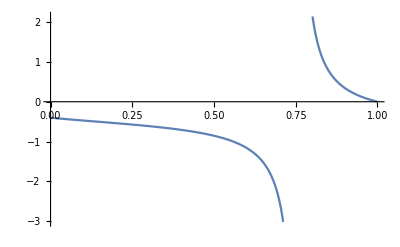

```mathematica
Plot[{rhoZeros⟦4⟧},{c,0,1}]
```

We will have nonnegative zero past the divergent c. The metric can also be pathological at -49c+32+8 c^2=0

```mathematica
c/.Solve[-49c+32+8 c^2==0,c]
```

{1/16 (49-9 √17),1/16 (49+9 √17)}

The first value is smaller than the limit imposed by the density function. We will take this to be the upper bound of our c.

## VII. Light Ring

```mathematica
veff=-2+r fDE1-r g'[r]/.μ->1/.Mu1DensCond⟦2⟧/.ϕ->Function[r,-M/(k r+a)]/.M->c a/.R->σ a/.σ->(1-c)/(3k)/.k->5/2/.a->1//Simplify
```

(16 c^6 (1+20 r+25 r^2)-2 (2+5 r)^4 (4-120 r+225 r^2)+16 c^5 (-24-230 r-25 r^2+250 r^3)+4 c^4 (312+1360 r-9150 r^2-6750 r^3+4375 r^4)+2 c (2+5 r)^2 (24-620 r-8150 r^2+12375 r^3+11250 r^4)-4 c^3 (368-9200 r^2+62500 r^3+83125 r^4+9375 r^5)+c^2 (528-640 r+62200 r^2+467000 r^3+20625 r^4-731250 r^5-281250 r^6))/((-1+c) (2+5 r) (-2+2 c+15 r) (4+4 c^2+40 r+75 r^2+4 c (-2+5 r)) (2 c^2-(2+5 r)^2+c (2+35 r+25 r^2)))

```mathematica
Series[r/.Solve[veff==0,r],{c,0,2}]//FullSimplify//Normal
```

Root::sbr: Because of branch cuts, the series may represent a different root of 128-192 c-528 c^2+1472 c^3-1248 c^4+384 c^5-16 c^6+(-2560+4000 c+640 c^2-5440 c^4+3680 c^5-320 c^6) #1+(-26400+88800 c-62200 c^2-36800 c^3+36600 c^4+400 c^5-400 c^6) #1^2+(-64000+258000 c-467000 c^2+250000 c^3+27000 c^4-4000 c^5) #1^3+«3»& for some values of c.

General::stop: Further output of Root::sbr will be suppressed during this calculation.

{-2/5-4/5 ⅈ √(1/11 (6+√3)) √c+4/605 (64+29 √3) c+(ⅈ (9961+11386 √3) c^(3/2))/(13310 √(11 (6+√3)))+(3 (97530+19687 √3) c^2)/805255,-2/5-4/5 ⅈ √(1/11 (6+√3)) √c+4/605 (64+29 √3) c+(ⅈ (9961+11386 √3) c^(3/2))/(13310 √(11 (6+√3)))+(3 (97530+19687 √3) c^2)/805255,-2/5-4/605 (-64+29 √3) c+(ⅈ √(6+√3) (-34158+9961 √3) c^(3/2))/439230-(3 (-97530+19687 √3) c^2)/805255+√c Root-0.498 ⅈRoot[768+4800 #1^2+6875 #1^4&,3]0.,-2/5+4/5 ⅈ √(1/11 (6-√3)) √c-4/605 (-64+29 √3) c+(ⅈ (34158-9961 √3) √(6+√3) c^(3/2))/439230-(3 (-97530+19687 √3) c^2)/805255,-2/15 (-2+√3)+((-47+61 √3) c)/3630-(3 (-93033+82303 √3) c^2)/1610510,2/15 (2+√3)+((-47-61 √3) c)/3630+(3 (93033+82303 √3) c^2)/1610510}

We can get r_LR/R.

```mathematica
Series[(r/.Solve[veff==0,r])/(2(1-c)/15),{c,0,2}]//FullSimplify//Normal
```

Root::sbr: Because of branch cuts, the series may represent a different root of 128-192 c-528 c^2+1472 c^3-1248 c^4+384 c^5-16 c^6+(-2560+4000 c+640 c^2-5440 c^4+3680 c^5-320 c^6) #1+(-26400+88800 c-62200 c^2-36800 c^3+36600 c^4+400 c^5-400 c^6) #1^2+(-64000+258000 c-467000 c^2+250000 c^3+27000 c^4-4000 c^5) #1^3+«3»& for some values of c.

General::stop: Further output of Root::sbr will be suppressed during this calculation.

{-3-6 ⅈ √(1/11 (6+√3)) √c+3/121 (7+58 √3) c+(3 ⅈ (-53927+738 √3) c^(3/2))/(5324 √(11 (6+√3)))+(3 (311224+213457 √3) c^2)/322102,-3-6 ⅈ √(1/11 (6+√3)) √c+3/121 (7+58 √3) c+(3 ⅈ (-53927+738 √3) c^(3/2))/(5324 √(11 (6+√3)))+(3 (311224+213457 √3) c^2)/322102,-3-3/121 (-7+58 √3) c-(3 ⅈ √(2+1/(√3)) (53927+738 √3) c^(3/2))/58564+((933672-640371 √3) c^2)/322102+√c Root-3.74 ⅈRoot[3888+432 #1^2+11 #1^4&,3]0.,-3+6 ⅈ √(1/11 (6-√3)) √c-3/121 (-7+58 √3) c+(3 ⅈ √(2+1/(√3)) (53927+738 √3) c^(3/2))/58564+((933672-640371 √3) c^2)/322102,2-√3+1/484 (921-423 √3) c+((515787-325935 √3) c^2)/161051,2+√3+3/484 (307+141 √3) c+(3 (171929+108645 √3) c^2)/161051}

To see if it matches Schwarzschild, note that r_LR=3 M_BH. Since R=M_BH/2 in vacuum, we have r_LR=6R. Observe that

```mathematica
Solve[6R==r(1+R/r)^2,r]//Expand//Simplify
```

{{r→-((-2+√3) R)},{r→(2+√3) R}}

The second solution matches our vacuum limit.